```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
?Evaluate
```

Evaluate[expr] causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.

```mathematica
f[omega_,eps_]:=1/(Sqrt[Pi]eps) Exp[-omega^2/eps^2]
```

```mathematica
table:=Table[f[omega,eps],{eps,0.1, 1.1, 0.1}]
```

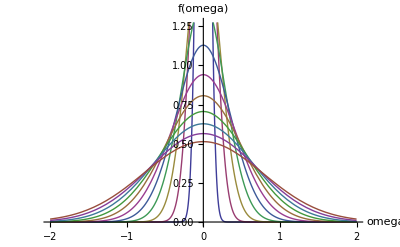

```mathematica
Plot[Evaluate[table],{omega,-2,2},AxesLabel->{"omega","f(omega)"}]
```

```mathematica
Integrate[f[omega,eps],{omega,-Infinity,Infinity}]
```

ConditionalExpression[1/(√(1/eps^2) eps),Re[1/eps^2]>0]